# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../../neupackage/mma/neutrino.wl"]
```

```mathematica
Get["../../../neupackage/mma/neumat.wl"]
```

```mathematica
colorpalette5={RGBColor[172,151,62],
RGBColor[129,118,204],
RGBColor[91,169,102],
RGBColor[199,90,147],
RGBColor[204,95,67]}
```

{RGBColor[172,151,62],RGBColor[129,118,204],RGBColor[91,169,102],RGBColor[199,90,147],RGBColor[204,95,67]}

```mathematica
markers=Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

## Rabi Oscillation

```mathematica
ampRabi[a_,k_,omegam_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2);
```

```mathematica
probRabi[a_,k_,omegam_,x_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2)Sin[(√(Abs[a]^2+(k-omegam)^2))/2 x]^2;
```

Parameters

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093]/2

lambdaN=0.25*Cos[2thetaV]*Cos[2thetaV]omegaV (*MeV*)
omegaM=OmegaMatter2[lambdaN,thetaV,omegaV](*MeV*)
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV))]/2,Pi]
```

1.3×10^-16

0.154948

2.94775×10^-17

1.02322×10^-16

0.198931

```mathematica
datafracStashFullTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaM],2]},{x,0,endpoint}];
(*datafracStashTicks[i_]:=Take[datafracStashFullTicks[i],{1,Length@datafracStashFullTicks[i],Floor[(Length@datafracStashFullTicks[i])/5]}];*)
datafracStashTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaM],2]},{x,0,endpoint,Floor[endpoint/5]}];
```

```mathematica
solutionLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]
```

```mathematica
solutionNeutrinoLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]
solutionLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]
solutionNeutrinoLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]
solutionSinLists[solutions_,endpointModule_,stepsize_]:=Module[{},
Table[{x,(Abs[psi2[x]]^2)/.First@solutions},{x,0,endpointModule,stepsize}]
]
```

## Functions

```mathematica
solNumInterference[kList_,lamList_,endpointModule_]:=Module[{sysM,lenM},
lenM=Length@kList;
sysM=I D[{psi1[x],psi2[x]},x]==((-1+Total@Table[lamList[[i]]Cos[2thetamV]Sin[kList[[i]]x],{i,1,lenM}])PauliMatrix[3]/2-(Total[Table[lamList[[n]]Sin[2thetamV]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[1]/2).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

NDSolve[sysM,{psi1,psi2},{x,0,endpointModule}]
]
```

```mathematica
probRabiInterference[lambdas_,k_,omegam_,x_]:=Module[{a,detuning},
a=lambdas*Sin[2thetamV]/2;
detuning=(k[[1]]-1)/a[[1]]+a[[2]]^2/( 2 a[[1]](k[[2]]-1) );

1/(1+detuning^2)Sin[(√(a[[1]]^2+(a[[1]]detuning)^2))/2 x]^2
]
probRabiInterference2[lambdas_,k_,omegam_,x_]:=Module[{a,detuning},
a={Tan[2thetamV](k[[1]])BesselJ[1,lambdas[[1]]Cos[2thetamV]/k[[1]]]BesselJ[0,lambdas[[2]]Cos[2thetamV]/k[[2]]],Tan[2thetamV](k[[2]])BesselJ[0,lambdas[[1]]Cos[2thetamV]/k[[1]]]BesselJ[1,lambdas[[2]]Cos[2thetamV]/k[[2]]]};

detuning=(k[[1]]-1)/a[[1]]+a[[2]]^2/( 2 a[[1]](k[[2]]-1) );

1/(1+detuning^2)Sin[(√(a[[1]]^2+(a[[1]]detuning)^2))/2 x]^2
]
probRabiInterference3[lambdas_,k_,omegam_,x_]:=Module[{a,detuning,dmp,dmm},
a=lambdas*Sin[2thetamV]/2;
dmp =a[[2]]^2/2/(1-k[[2]]) ;
dmm =a[[2]]^2/2/(1+k[[2]]) ;

detuning=Abs[
(k[[1]] -( 1 + (dmp+dmm) ) )/a[[1]]
];

1/(1+detuning^2)Sin[(√(a[[1]]^2+(a[[1]]detuning)^2))/2 x]^2
]
```

```mathematica
??bNList
```

Calculate the b coefficient of the Hamiltonian; Example, bNList[listOfN,listOfWaveNumber,listOfAmplitude,listOfPhase,thetam]. Output is in unit of ω_m

bNList[neumat`Private`listOfN_,neumat`Private`listOfWaveNumber_,neumat`Private`listOfAmplitude_,neumat`Private`listOfPhase_,neumat`Private`thetam_]:=-(-ⅈ)^Total[neumat`Private`listOfN] Tan[2 neumat`Private`thetam] neumat`Private`listOfN.neumat`Private`listOfWaveNumber Times@@MapThread[BesselJ[#1,(#3 Cos[2 neumat`Private`thetam])/#2]&,{neumat`Private`listOfN,neumat`Private`listOfWaveNumber,neumat`Private`listOfAmplitude}]

## Single Frequency

```mathematica
10^(-4)Sin[2thetamV]/2
```

0.0000193725

```mathematica
endpointSin=400000

k11={1};
lam11={0.0001};

k12={1-2*10^5};
lam12={0.0001};

k13={1-10^(-4)};
lam13={0.0001};

k1List={k11,k12,k13};
lam1List={lam11,lam12,lam13};
```

400000

```mathematica
solNumSinAll=Table[solNumInterference[k1List[[i]],lam1List[[i]],endpointSin],{i,1,Length@k1List}]
```

{{{psi1→InterpolatingFunction[{{0., 400000.}}, <>],psi2→InterpolatingFunction[{{0., 400000.}}, <>]}},{{psi1→InterpolatingFunction[{{0., 400000.}}, <>],psi2→InterpolatingFunction[{{0., 400000.}}, <>]}},{{psi1→InterpolatingFunction[{{0., 400000.}}, <>],psi2→InterpolatingFunction[{{0., 400000.}}, <>]}}}

```mathematica
solsSin=solutionLists[solNumSinAll,endpointSin,100];
```

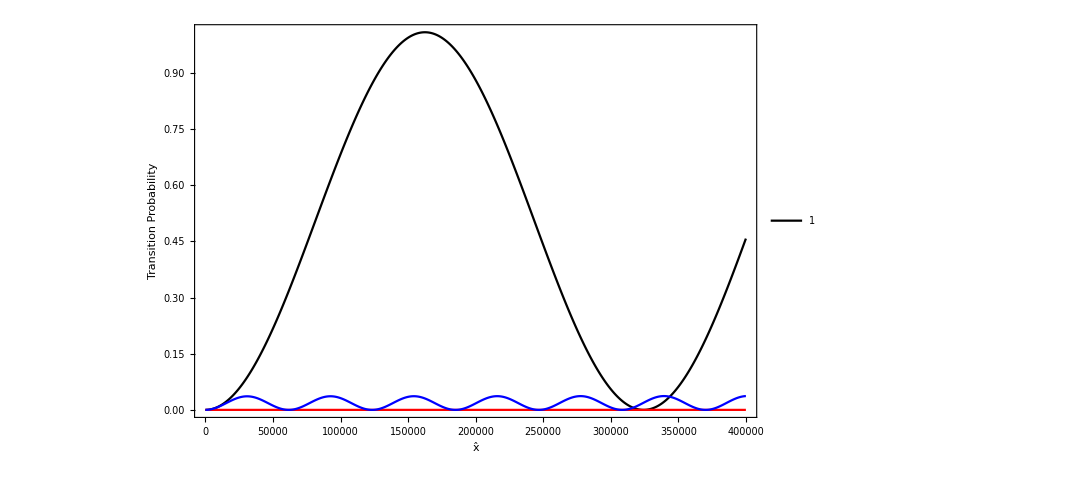

```mathematica
solsSinPlt=ListPlot[
solsSin
,Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
PlotRange->{Automatic,Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},Joined->False,PlotLegends->{1}]
```

## Multi-frequency

Solve the values need for the second frequency

```mathematica
Table[Solve[1+x^2==1/amp,x],{amp,{0.8,0.4}}]
```

{{{x→-0.5},{x→0.5}},{{x→-1.22474},{x→1.22474}}}

```mathematica
Solve[
(lam2*Sin[2thetamV]/2)^2/( 2(0.001*Sin[2thetamV]/2)Abs@(10-1) )==0.5,
lam2
]

Solve[
(0.2*Sin[2thetamV]/2)^2/( 2(xk1*Sin[2thetamV]/2)Abs@(10-1) )==1.22,
xk1
]

cc=(Sin[2thetamV]/2/2/0.001)

1-cc 0.02^2/1.22
```

{{lam2→-0.215541},{lam2→0.215541}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xk1→0.000352868}}

96.8623

0.968242

```mathematica
endpointMul=400000;
```

```mathematica
kListNeu1={1,0.1};
aListNeu1={0.0001,0.032}

(*For small k2*)

kListNeu2={1,10};
aListNeu2={0.0001,0.1}

(*For large k2>k1*)

kListNeu3={1,10};
aListNeu3={0.0001,0.05}
```

{0.0001,0.032}

{0.0001,0.1}

{0.0001,0.05}

```mathematica
kListNeu={kListNeu1,kListNeu2};
aListNeu={aListNeu1,aListNeu2};
(*kListNeu={kListNeu1,kListNeu2,kListNeu3};
aListNeu={aListNeu1,aListNeu2,aListNeu3};*)
```

```mathematica
(*solNumNeutrinoAll=Table[solNum[kListNeu[[i]],aListNeu[[i]],{0,0},thetamV,endpointMul],{i,1,Length@kListNeu}]*)
```

```mathematica
(*solsNeutrino=solutionNeutrinoLists[solNumNeutrinoAll,endpointMul,100];*)
```

```mathematica
(*solsNeutrinoPlt=ListPlot[
solsNeutrino
,Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
(*GridLines->{None, gridlinesList[[1;;4]]},*)PlotRange->{(*{0,2 10^5}*)Automatic,Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},Joined->False,PlotLegends->{1,2,3}]*)
```

```mathematica
solNumInterferenceAll=Table[solNumInterference[kListNeu[[i]],aListNeu[[i]],endpointMul],{i,1,Length@kListNeu}]
```

{{{psi1→InterpolatingFunction[{{0., 400000.}}, <>],psi2→InterpolatingFunction[{{0., 400000.}}, <>]}},{{psi1→InterpolatingFunction[{{0., 400000.}}, <>],psi2→InterpolatingFunction[{{0., 400000.}}, <>]}}}

```mathematica
solsInterference=solutionLists[solNumInterferenceAll,endpointMul,100];
```

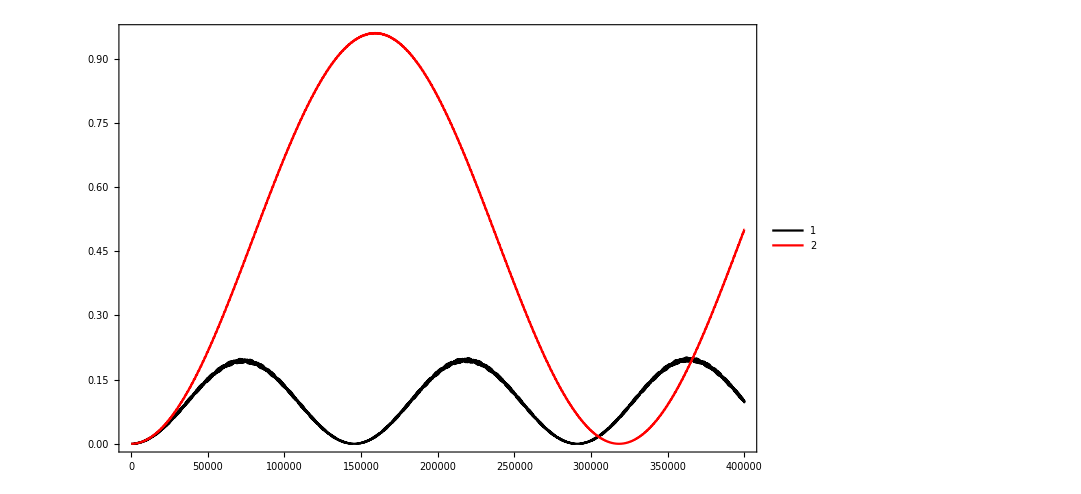

```mathematica
solsInterferencePlt=ListPlot[
solsInterference
,Joined->True,ImageSize->imgsize,Frame->True,
(*GridLines->{None, gridlinesList[[1;;4]]},*)PlotRange->{(*{0,2 10^5}*)Automatic,Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},Joined->False,PlotLegends->{1,2,3}]
```

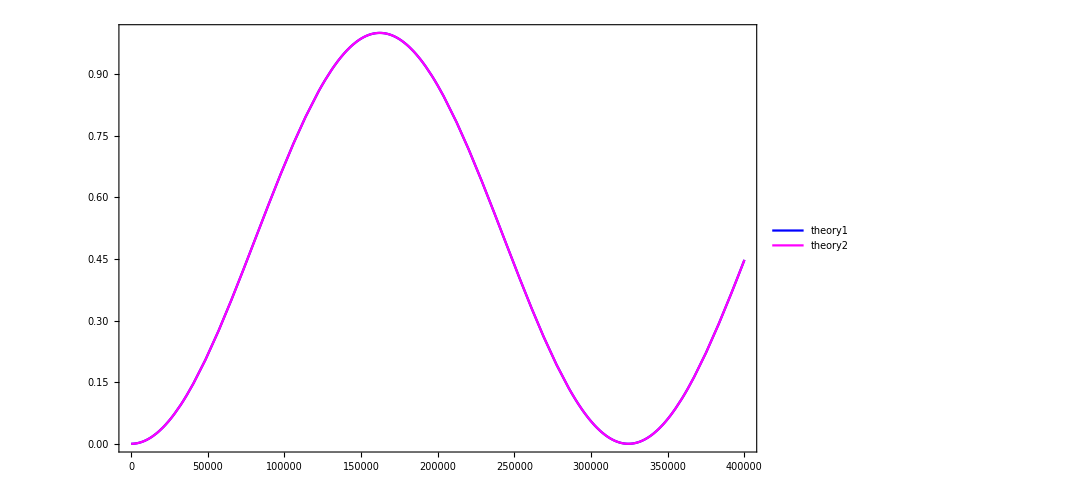

```mathematica
theoryOnePlt=Plot[Evaluate@{
(*probRabiInterference[aListNeu1,kListNeu1,1,x],*)
probRabi[aListNeu1[[1]]Sin[2thetamV]/2,kListNeu1[[1]],1,x],
(*probRabiInterference[aListNeu2,kListNeu2,1,x],*)
probRabi[aListNeu2[[1]]Sin[2thetamV]/2,kListNeu2[[1]],1,x],(*
probRabiInterference[aListNeu3,kListNeu3,1,x]*)
},{x,0,endpointMul},PlotStyle->{Blue,Magenta,Cyan,Yellow,Green,Black,Red,},ImageSize->imgsize,Frame->True,PlotLegends->{"theory1","theory2"}
]
```

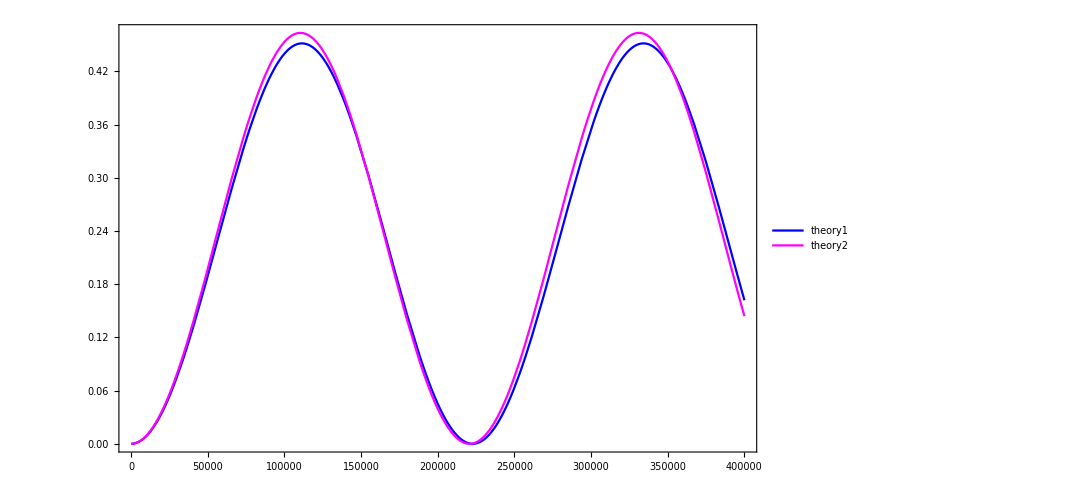

```mathematica
theoryInterferencePlt=Plot[Evaluate@{
(*probRabiInterference[aListNeu1,kListNeu1,1,x],*)
probRabiInterference2[aListNeu1,kListNeu1,1,x],
(*probRabiInterference[aListNeu2,kListNeu2,1,x],*)
probRabiInterference2[aListNeu2,kListNeu2,1,x],(*
probRabiInterference[aListNeu3,kListNeu3,1,x]*)
},{x,0,endpointMul},PlotStyle->{Blue,Magenta,Cyan,Yellow,Green,Black,Red,},ImageSize->imgsize,Frame->True,PlotLegends->{"theory1","theory2"}
]
```

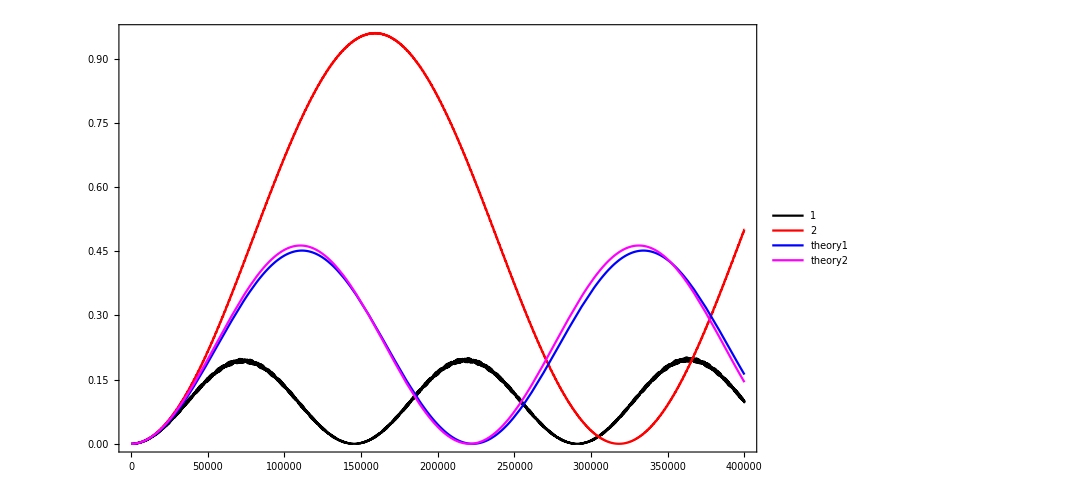

```mathematica
Show[solsInterferencePlt,theoryInterferencePlt]
```

```mathematica
dOrderedList2=qValueOrderdList[listNGenerator[2,4],kListNeu1,aListNeu1,{0,0},thetamV]//Grid
```

{1,0} | 0.
{0,1} | 146.771
{0,-1} | 179.387
{0,2} | 881.269
{0,-2} | 1321.9
{0,3} | 10436.6
{0,-3} | 19382.2
{1,1} | 32163.
{1,-1} | 39310.3
{-1,0} | 105523.
{0,4} | 181744.
{0,-4} | 424069.
{-1,-1} | 675422.
{-1,1} | 746896.
{1,2} | 796613.
{1,-2} | 1.19492×10^6
{-1,-2} | 8.76274×10^6
{-1,2} | 1.07543×10^7
{1,3} | 2.23928×10^7
{1,-3} | 4.15867×10^7
{-1,-3} | 1.71678×10^8
{-1,3} | 2.35658×10^8
{1,4} | 7.51018×10^8
{2,0} | 1.14463×10^9
{1,-4} | 1.75238×10^9
{-2,0} | 3.4339×10^9
{-1,-4} | 4.50611×10^9
{-1,4} | 7.00951×10^9
{2,-1} | 7.2714×10^9
{2,1} | 8.04086×10^9
{-2,-1} | 2.26606×10^10
{-2,1} | 2.34301×10^10
{2,-2} | 9.21715×10^10
{2,2} | 1.1312×10^11
{-2,-2} | 3.01652×10^11
{-2,2} | 3.226×10^11
{2,-3} | 1.73365×10^12
{2,3} | 2.37973×10^12
{-2,-3} | 6.04085×10^12
{-2,3} | 6.68693×10^12
{2,-4} | 4.27691×10^13
{2,4} | 6.65297×10^13
{3,0} | 9.93292×10^13
{-2,-4} | 1.61572×10^14
{-2,4} | 1.85333×10^14
{-3,0} | 1.98658×10^14
{3,-1} | 6.54571×10^14
{3,1} | 6.76797×10^14
{-3,-1} | 1.32137×10^15
{-3,1} | 1.34359×10^15
{3,-2} | 8.67691×10^15
{3,2} | 9.27947×10^15
{-3,-2} | 1.77154×10^16
{-3,2} | 1.83179×10^16
{3,-3} | 1.72532×10^17
{3,3} | 1.90984×10^17
{-3,-3} | 3.57057×10^17
{-3,3} | 3.7551×10^17
{3,-4} | 4.56791×10^18
{3,4} | 5.23966×10^18
{-3,-4} | 9.60604×10^18
{4,0} | 9.69705×10^18
{-3,4} | 1.02778×10^19
{-4,0} | 1.61618×10^19
{4,-1} | 6.44681×10^19
{4,1} | 6.55525×10^19
{-4,-1} | 1.07844×10^20
{-4,1} | 1.08929×10^20
{4,-2} | 8.63049×10^20
{4,2} | 8.92404×10^20
{-4,-2} | 1.45016×10^21
{-4,2} | 1.47951×10^21
{4,-3} | 1.73522×10^22
{4,3} | 1.8249×10^22
{-4,-3} | 2.9309×10^22
{-4,3} | 3.02058×10^22
{4,-4} | 4.65213×10^23
{4,4} | 4.97745×10^23
{-4,-4} | 7.90537×10^23
{-4,4} | 8.23069×10^23
{0,0} | ComplexInfinity

```mathematica
nlistInterference=Table[solNList[{{1,0},{0,1},{0,-1}},kListNeu[[i]],aListNeu[[i]],{0,0},thetamV,endpointMul],{i,1,Length@kListNeu}]
```

{{{neumat`Private`psi1→InterpolatingFunction[{{0., 400000.}}, <>],neumat`Private`psi2→InterpolatingFunction[{{0., 400000.}}, <>]}},{{neumat`Private`psi1→InterpolatingFunction[{{0., 400000.}}, <>],neumat`Private`psi2→InterpolatingFunction[{{0., 400000.}}, <>]}}}

```mathematica
nlistInterferenceAll=solutionNeutrinoLists[nlistInterference,endpointMul,100]
```

{{{0,0.},{100,0.0000173731},{200,0.0000306125},{300,0.00003725},{400,0.0000617273},{500,9.32092×10^-6},3989,{399500,0.131309},{399600,0.129271},{399700,0.132553},{399800,0.130673},{399900,0.127488},{400000,0.131683}},{1}}
 |  |  |  |

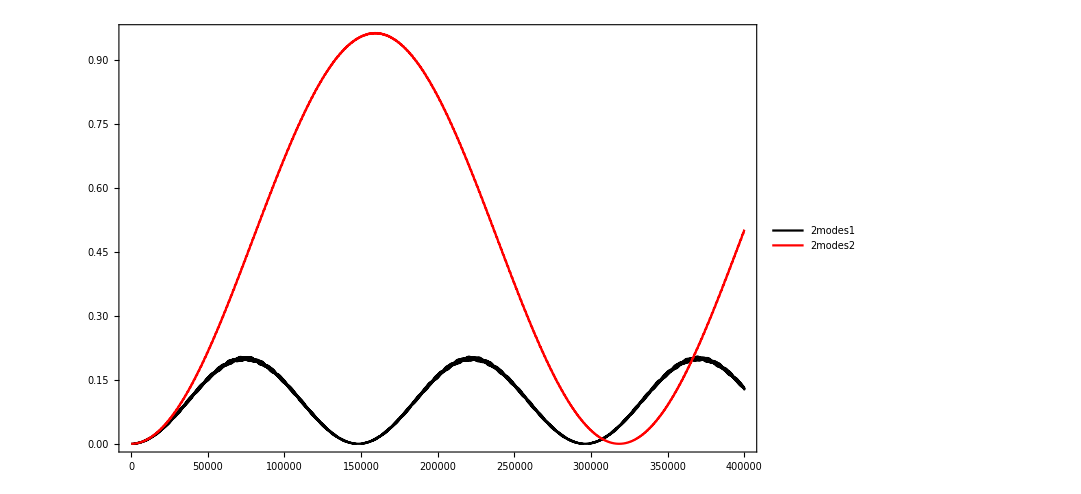

```mathematica
nlistInterferencePlt=ListPlot[
nlistInterferenceAll
,Joined->True,ImageSize->imgsize,Frame->True,
PlotRange->{Automatic,Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},Joined->False,PlotLegends->{"2modes1","2modes2"}]
```

```mathematica
nlistInterference2=Table[solNList[{{1,0},{0,1}},kListNeu[[i]],aListNeu[[i]],{0,0},thetamV,endpointMul],{i,1,Length@kListNeu}]
```

{{{neumat`Private`psi1→InterpolatingFunction[{{0., 400000.}}, <>],neumat`Private`psi2→InterpolatingFunction[{{0., 400000.}}, <>]}},{{neumat`Private`psi1→InterpolatingFunction[{{0., 400000.}}, <>],neumat`Private`psi2→InterpolatingFunction[{{0., 400000.}}, <>]}}}

```mathematica
nlistInterference2All=solutionNeutrinoLists[nlistInterference2,endpointMul,100]
```

{{{0,0.},{100,0.0000403257},{200,0.0000302792},{300,5.12993×10^-6},{400,0.0000691886},{500,0.0000404278},3989,{399500,0.164986},{399600,0.164144},{399700,0.167471},{399800,0.16354},{399900,0.161965},{400000,0.165514}},{1}}
 |  |  |  |

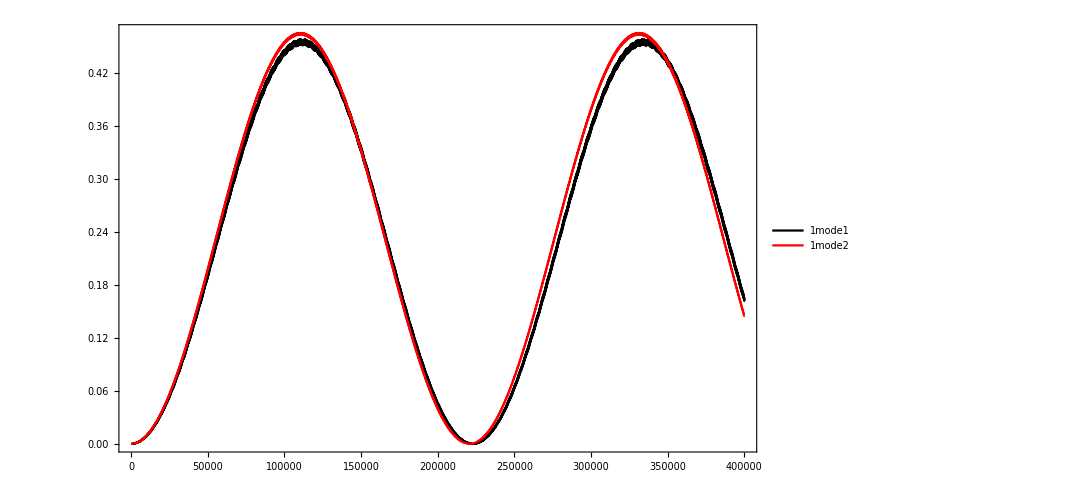

```mathematica
nlistInterference2Plt=ListPlot[
nlistInterference2All
,Joined->True,ImageSize->imgsize,Frame->True,
PlotRange->{Automatic,Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},Joined->False,PlotLegends->{"1mode1","1mode2"}]
```

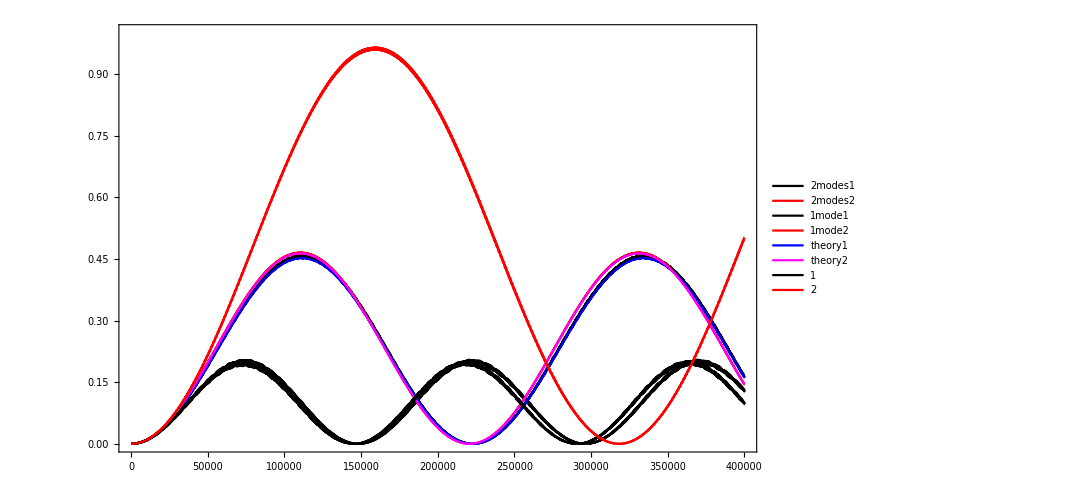

```mathematica
Show[nlistInterferencePlt,nlistInterference2Plt,theoryInterferencePlt,solsInterferencePlt,PlotRange->{Automatic,{0,1}}]
```

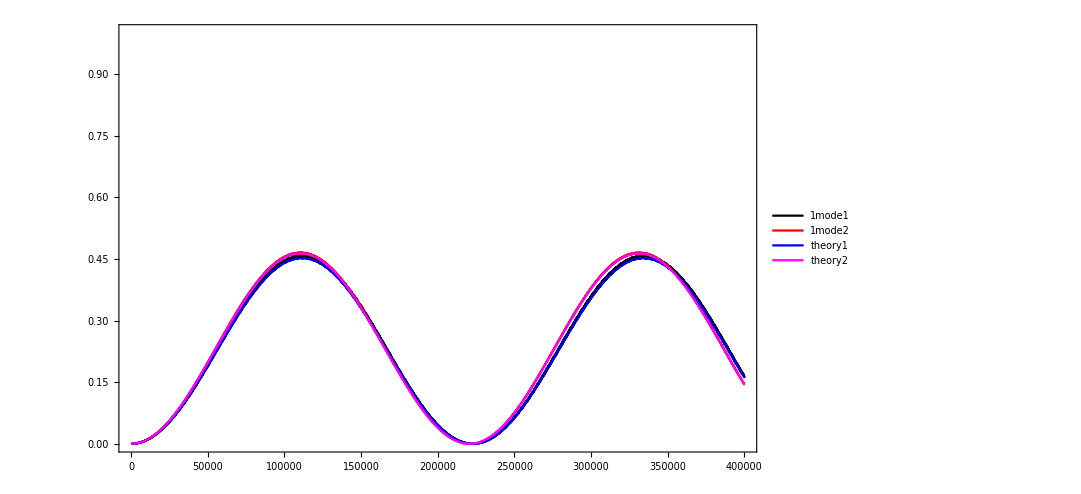

```mathematica
Show[nlistInterference2Plt,theoryInterferencePlt,PlotRange->{Automatic,{0,1}}]
```

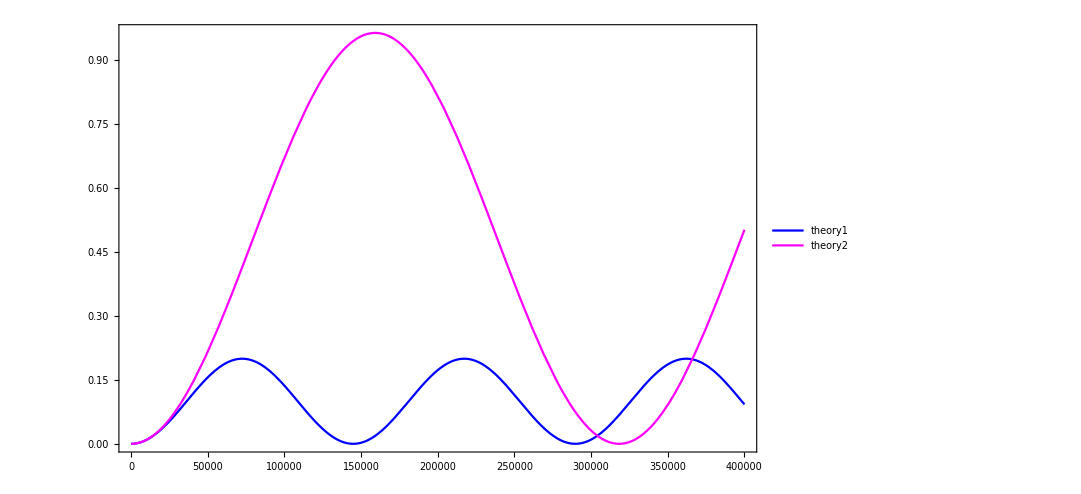

```mathematica
theoryInterferencePlt2=Plot[Evaluate@{
probRabiInterference3[aListNeu1,kListNeu1,1,x],
probRabiInterference3[aListNeu2,kListNeu2,1,x],(*
probRabiInterference[aListNeu3,kListNeu3,1,x]*)
},{x,0,endpointMul},PlotStyle->{Blue,Magenta,Cyan,Yellow,Green,Black,Red,},ImageSize->imgsize,Frame->True,PlotLegends->{"theory1","theory2"}
]
```

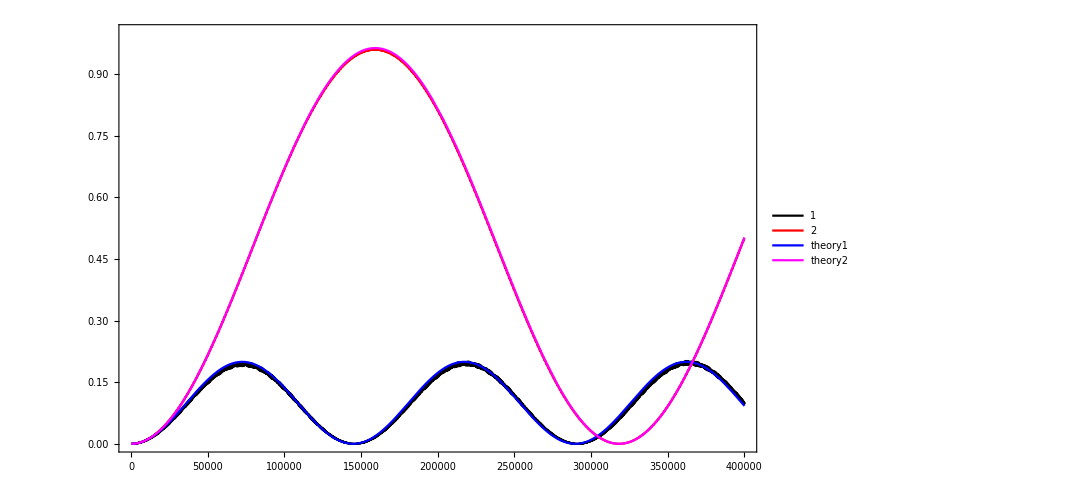

```mathematica
Show[solsInterferencePlt,theoryInterferencePlt2,PlotRange->{Automatic,{0,1}}]
```

```mathematica
Export["higher-order/first2modes-a1-1e-4-k1-1-a2-"<>ToString@aListNeu1[[2]]<>"-k2-"<>ToString@kListNeu1[[2]]<>".csv",nlistInterference2All[[1]]]
Export["higher-order/first2modes-a1-1e-4-k1-1-a2-"<>ToString@aListNeu2[[2]]<>"-k2-"<>ToString@kListNeu2[[2]]<>".csv",nlistInterference2All[[2]]]
```

higher-order/first2modes-a1-1e-4-k1-1-a2-0.032-k2-0.1.csv

higher-order/first2modes-a1-1e-4-k1-1-a2-0.1-k2-10.csv

```mathematica
Export["higher-order/first3modes-a1-1e-4-k1-1-a2-"<>ToString@aListNeu1[[2]]<>"-k2-"<>ToString@kListNeu1[[2]]<>".csv",nlistInterferenceAll[[1]]]
Export["higher-order/first3modes-a1-1e-4-k1-1-a2-"<>ToString@aListNeu2[[2]]<>"-k2-"<>ToString@kListNeu2[[2]]<>".csv",nlistInterferenceAll[[2]]]
```

higher-order/first3modes-a1-1e-4-k1-1-a2-0.032-k2-0.1.csv

higher-order/first3modes-a1-1e-4-k1-1-a2-0.1-k2-10.csv

```mathematica
Export["higher-order/theory2-a1-1e-4-k1-1-a2-"<>ToString@aListNeu1[[2]]<>"-k2-"<>ToString@kListNeu1[[2]]<>".csv",Table[{i,probRabiInterference2[aListNeu1,kListNeu1,1,i]},{i,1,endpointMul,100}]]
Export["higher-order/theory2-a1-1e-4-k1-1-a2-"<>ToString@aListNeu2[[2]]<>"-k2-"<>ToString@kListNeu2[[2]]<>".csv",Table[{i,probRabiInterference2[aListNeu2,kListNeu2,1,i]},{i,1,endpointMul,100}]]
```

higher-order/theory2-a1-1e-4-k1-1-a2-0.032-k2-0.1.csv

higher-order/theory2-a1-1e-4-k1-1-a2-0.1-k2-10.csv

```mathematica
Export["higher-order/theory3-a1-1e-4-k1-1-a2-"<>ToString@aListNeu1[[2]]<>"-k2-"<>ToString@kListNeu1[[2]]<>".csv",Table[{i,probRabiInterference3[aListNeu1,kListNeu1,1,i]},{i,1,endpointMul,100}]]
Export["higher-order/theory3-a1-1e-4-k1-1-a2-"<>ToString@aListNeu2[[2]]<>"-k2-"<>ToString@kListNeu2[[2]]<>".csv",Table[{i,probRabiInterference3[aListNeu2,kListNeu2,1,i]},{i,1,endpointMul,100}]]
```

higher-order/theory3-a1-1e-4-k1-1-a2-0.032-k2-0.1.csv

higher-order/theory3-a1-1e-4-k1-1-a2-0.1-k2-10.csv

```mathematica
Export["higher-order/full-a1-1e-4-k1-1-a2-"<>ToString@aListNeu1[[2]]<>"-k2-"<>ToString@kListNeu1[[2]]<>".csv",solsInterference[[1]]]
Export["higher-order/full-a1-1e-4-k1-1-a2-"<>ToString@aListNeu2[[2]]<>"-k2-"<>ToString@kListNeu2[[2]]<>".csv",solsInterference[[2]]]
```

higher-order/full-a1-1e-4-k1-1-a2-0.032-k2-0.1.csv

higher-order/full-a1-1e-4-k1-1-a2-0.1-k2-10.csv

```mathematica
Export["higher-order/rabi-one-a1-1e-4-k1-1-a2-"<>ToString@aListNeu1[[2]]<>"-k2-"<>ToString@kListNeu1[[2]]<>".csv",Table[{i,probRabi[aListNeu1[[1]]Sin[2thetamV]/2,kListNeu1[[1]],1,i]},{i,1,endpointMul,100}]
]
Export["higher-order/rabi-one-a1-1e-4-k1-1-a2-"<>ToString@aListNeu2[[2]]<>"-k2-"<>ToString@kListNeu2[[2]]<>".csv",Table[{i,probRabi[aListNeu2[[1]]Sin[2thetamV]/2,kListNeu2[[1]],1,i]},{i,1,endpointMul,100}] 
]
```

higher-order/rabi-one-a1-1e-4-k1-1-a2-0.032-k2-0.1.csv

higher-order/rabi-one-a1-1e-4-k1-1-a2-0.1-k2-10.csv